# Correlation Sampling - General Process

## Last Updated: 2025/10/24 v1.1.4

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: better document existing stuff, e.g. linewidth vs time, e.g. # of points*)
```

```mathematica
(*todo: add parameter table - this should be our main processing instead of matlab*)
```

# General

## Import

```mathematica
(*memory management etc*)
Needs["Utilities`CleanSlate`"]
```

```mathematica
(*(*cleanup and return*)
Remove[resVar,tempVar];ClearSystemCache[];ClearInOut;*)
```

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

## Plot Options

```mathematica
(*set plot options - analytical*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogLogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set plot options - list*)
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

```mathematica
(*set exotic plot options*)
SetOptions[DateListPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
```

### Ensure Parallel Kernels Have Plotting Options Set

```mathematica
(*extend plot options to parallel kernels*)
ParallelEvaluate[
(*set plot options - analytical*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogLogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];

(*set plot options - list*)
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];

(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

## Plot Creation

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Clayton List Plot

```mathematica
(*todo: document*)
(*todo: improve with options etc*)
PlotTMP[datasets_Association,xLabel_String,yLabel_String,Title_String]:=With[
{
dsAct=Riffle[#,#]&[Values[datasets]],
dsLegend=Riffle[ConstantArray[None,Length[datasets]],Keys[datasets]],
dsPlotStyles=Riffle[
{DefaultPlotColors[[#]],PointSize[0.011]}&/@Range[Length[datasets]],
{DefaultPlotColors[[#]],Dashed,Thickness[0.004]}&/@Range[Length[datasets]]
]
},

Return[
ListPlot[
dsAct,

PlotRange->{
{Full,Full},
{Full,Full}
},

(*plot formatting*)
PlotRangePadding->False,
FrameTicksStyle->Directive[Black,20],
FrameLabel->{ 
{Style[yLabel,{Black,Directive[15]}],None},
{
Style[xLabel,{Black,Directive[15]}],
Style[Title,{Black,Directive[15]}]
}
},

(*labelling*)
(*PlotLabels->Placed[
{
Style["PRECISION",{DefaultPlotColors[[1]],Directive[15]}],
None
},
{{Scaled[0.7],Before}}
],*)
PlotLegends->dsLegend,
PlotStyle->dsPlotStyles,
Joined->Riffle[
ConstantArray[True,Length[datasets]],
ConstantArray[False,Length[datasets]]
],

(*size output image*)
AspectRatio->Full,
ImageSize->{800,500}
]
];
];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[NonlinearModelFit::lstol];
Off[NonlinearModelFit::fmgz];
Off[NonlinearModelFit::bddir];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
Off[Syntax::stresc];
];
```

```mathematica
(*turn upsetting things off*)
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[NonlinearModelFit::lstol];
Off[NonlinearModelFit::fmgz];
Off[NonlinearModelFit::bddir];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
Off[Syntax::stresc];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Scaling Fits

```mathematica
(*
power-law fit function
used here mostly for ADEV trendline fitting
*)
FitPowerFunc[dataset_]:=Block[{
A,x,K,B,
guessK,guessA,
logData=Log[dataset]
},

(*guess parameter values*)
guessK=Mean[(#[[;;,2]])/(#[[;;,1]])]&[logData[[2;;]]-logData[[;;-2]]];
guessA=Exp[Mean[logData[[;;,2]]-guessK*logData[[;;,1]]]];

(*do fit!*)
Return[
NonlinearModelFit[dataset,
{A*x^K},
{{A,guessA},
{K,guessK}},
x
]
];
];
```

```mathematica
(*
linear fit function
used here mostly for ADEV trendline fitting
*)
FitLinearFunc[dataset_]:=Block[{
x
},

Return[
LinearModelFit[Log[dataset],
{x},
x
]
];
];
```

## FFT Processing: FFTBlockFit

```mathematica
(*FFTBlockFit: directly process data & fit FFT with lorentzian*)
Clear[FFTBlockFit];
Options[FFTBlockFit]={
(*method to use for NonlinearModelFit*)
"FitMethod"->"ConjugateGradient",

(*fudge factors for initial guesses for {A,Γ,f}*)
"FitFudgeArray"->{1.,1.,0.},

(*number of points about peak to use for fitting*)
"PeakFitNumPoints"->-1
};
```

```mathematica
(*implement FFTBlockFit*)
FFTBlockFit[
data_List,
OptionsPattern[]
]:=Block[{
(*use block to define local variables*)
A,Γ,x,f,

(*extract user configured parameters*)
fitMethod=OptionValue["FitMethod"],
fitFudgeArr=OptionValue["FitFudgeArray"]
},

Module[{
(*helper variables*)
numSamplePoints=Length[data],
tmax=data[[-1,1]]-data[[1,1]],
fmax=1./Mean[data[[2;;,1]]-data[[1;;-2,1]]],

(*fft-related*)
dataFFTMag,

(*lorentzian fitting*)
fitGuess,peakIndDJ,fitRes,Γguess,
peakFitIndMin,peakFitIndMax
},

(*do FFT*)
dataFFTMag=Transpose[{
(*fft freqs - x-axis*)
Range[0,fmax/2.,fmax/(numSamplePoints-1)][[;;IntegerPart[numSamplePoints/2.]]],

(*fft values - power (i.e. ampl^2)*)
Abs[
Fourier[
data[[;;,2]]-Mean[data[[;;,2]]],
FourierParameters->{1,-1}
][[;;IntegerPart[numSamplePoints/2.]]]
]^2.
}];


(*prepare fitting*)
peakIndDJ=First@Ordering[dataFFTMag[[;;,2]],-1];
Γguess=0.5/tmax*Sqrt[2];
fitGuess={
{A,Abs[Subtract@@{dataFFTMag[[peakIndDJ,2]],Min[dataFFTMag[[;;,2]]]}]*Γguess^1.*fitFudgeArr[[1]]},
{Γ,Γguess^1.*fitFudgeArr[[2]]},
{f,dataFFTMag[[peakIndDJ,1]]+(fmax/(numSamplePoints-1)*fitFudgeArr[[3]])}
};

(*get points to use for fit*)
If[OptionValue["PeakFitNumPoints"]>=1,
(*true case: use valid PeakFitNumPoints*)
{peakFitIndMin,peakFitIndMax}={
Max[1,peakIndDJ-OptionValue["PeakFitNumPoints"]],
Min[Length[dataFFTMag],peakIndDJ+OptionValue["PeakFitNumPoints"]]
};,

(*false case: use full range*)
{peakFitIndMin,peakFitIndMax}={1,-1};
];


(*do fit*)
fitRes=NonlinearModelFit[
(*raw data*)
dataFFTMag[[peakFitIndMin;;peakFitIndMax]],

(*fit function*)
{A*Γ/(Γ^2.+(x-f)^2.)},

(*fit guesses*)
fitGuess,

(*fit variable*)
x,

(*configure solving*)
MaxIterations->Automatic,
Method->fitMethod
];

(*return both the processed data and the fitted result*)
Return[
{dataFFTMag,fitGuess,fitRes}
];
]];
```

## FFT Plot #1: FFTBlockPlot (Uses FFTBlockFit)

```mathematica
(*function that takes raw time-series data, then calls FFTBlockFit, then plots fit with raw*)
Clear[FFTBlockPlot];
Options[FFTBlockPlot]={
(*method to use for NonlinearModelFit*)
"FitMethod"->"ConjugateGradient",

(*fudge factors for initial guesses for {A,Γ,f}*)
"FitFudgeArray"->{1.,1.,0.},

(*number of points about peak to use for fitting*)
"PeakFitNumPoints"->-1
};
```

```mathematica
(*implement FFTBlockPlot*)
FFTBlockPlot[
data_List,
OptionsPattern[]
]:=Block[
{
A,Γ,f,x,
(*extract user configured parameters*)
fitMethod=OptionValue["FitMethod"],
fitFudgeArr=OptionValue["FitFudgeArray"]
},

Module[
{
(*get FFT and fitted data*)
dataProcRes=FFTBlockFit[
data,
"FitMethod"->fitMethod,
"FitFudgeArray"->fitFudgeArr,
"PeakFitNumPoints"->OptionValue["PeakFitNumPoints"]
],
dataFFTMag,fitGuess,fitRes,
fftStepSize,

(*plots*)
fitModel=A*Γ/(Γ^2+(x-f)^2),
fitGuessModel,fitPlotMinF,fitPlotMaxF,
plotDataFFTMag,plotFittedFFTMag,fitParams
},

(*expand dataProcRes*)
{dataFFTMag,fitGuess,fitRes}=dataProcRes;
(*calculate FFT step size for convenience*)
fftStepSize=(2.*dataFFTMag[[-1,1]])/(Length[dataFFTMag]-1);(*2x max freq in dataFFTMag b/c nyquist*)
(*process fit parameters into something nice*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];


(*create raw plot*)
plotDataFFTMag=ListPlot[
{
dataFFTMag,
dataFFTMag
},

PlotRange->{
{Full,Full},
{Full,Full}
},
PlotRangePadding->False,

FrameLabel->{
 {Style["Power (Ampl^2)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp FFT (RID: "<>ToString[rid]<>")",{Black,Directive[15]}]
}
},

Joined->{
False,True
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.011]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.004]}
},

PlotLegends->{
"FFT Data - Ampl^2"
},

ImageSize->Scaled[0.45],
PerformanceGoal->"Speed"
(*MaxPlotPoints->IntegerPart[1.*^4]*)
];


(*create function to plot initial guess*)
fitGuessModel=fitModel/.{A->fitGuess[[1,2]],Γ->fitGuess[[2,2]],f->fitGuess[[3,2]]};

(*adjust plot range to capture only important parts of the lorentzian*)
fitPlotMinF=Max[
(f/.fitRes["BestFitParameters"])-(fftStepSize*Length[dataFFTMag]^0.6),
fftStepSize*1.
];
fitPlotMaxF=Max[
(f/.fitRes["BestFitParameters"])+(fftStepSize*Length[dataFFTMag]^0.6),
fftStepSize*1.
];

(*plot fitted lorentzian!*)
plotFittedFFTMag=Plot[
{
fitRes[x],
fitGuessModel
},
{x,fitPlotMinF,fitPlotMaxF},

(*PlotRange->Full,*)
PlotRange->{
{Full,Full},
{Full,Max[dataFFTMag[[;;,2]]]}
},

(*focus plotting around important points*)
PlotPoints->{2000,{(f/.fitRes["BestFitParameters"])}},
(*PlotPoints->{5000,lorentzianExtraPlotPoints},*)

PlotStyle->{
{Red,Thickness[0.003],Opacity[0.88]},
{Green,Thickness[0.003],Opacity[0.88]}
},
PlotLegends->{
"Lorentzian NLSQ Fit",
"Initial Guess"
},

PerformanceGoal->"Quality"
];


(*return results*)
Return[
{
(*numerical data*)
{dataFFTMag,fitGuess,fitRes},

(*pretty plots*)
{fitParams,plotDataFFTMag,plotFittedFFTMag}
}
];
]]
```

## FFT Plot #2: FFTBlockPlotNicer (Uses FFTBlockPlot, which in turn uses FFTBlockFit)

```mathematica
(*tmp batch display function*)
Clear[FFTBlockPlotNicer];
Options[FFTBlockPlotNicer]={
(*method to use for NonlinearModelFit*)
"FitMethod"->"ConjugateGradient",

(*fudge factors for initial guesses for {A,Γ,f}*)
"FitFudgeArray"->{1.,1.,0.},

(*number of points about peak to use for fitting*)
"PeakFitNumPoints"->-1
};
```

```mathematica
(*tmp batch display function*)
FFTBlockPlotNicer[
datasetRaw_List,
OptionsPattern[]
]:=Module[
{
localDataDJ=FFTBlockPlot[
datasetRaw,
"FitMethod"->OptionValue["FitMethod"],
"FitFudgeArray"->OptionValue["FitFudgeArray"],
"PeakFitNumPoints"->OptionValue["PeakFitNumPoints"]
],

dataFFTMagDJ,fitGuessDJ,fitResDJ,
fitParamsDJ,plotDataFFTMagDJ,plotFittedFFTMagDJ,

resString,summaryPlot,
freqSpanShowMin,freqSpanShowMax,peakIndDJ,

tmpPointsSpan=20
},

(*break out results*)
{dataFFTMagDJ,fitGuessDJ,fitResDJ}=localDataDJ[[1,{1,2,3}]];
{fitParamsDJ,plotDataFFTMagDJ,plotFittedFFTMagDJ}=localDataDJ[[2,{1,2,3}]];

(*points around peak to show: about 100*)
peakIndDJ=First@Ordering[dataFFTMagDJ[[;;,2]],-1];
freqSpanShowMin=Max[1,peakIndDJ-tmpPointsSpan];
freqSpanShowMax=Min[peakIndDJ+tmpPointsSpan,Length[dataFFTMagDJ]];

(*print freq precision*)
resString=StringForm["Linecenter Precision: `` μHz",NumberForm[Abs[1.*^6*Subtract@@fitResDJ["ParameterConfidenceIntervals"][[3]]],{∞,3}]];

(*create summary plot*)
summaryPlot=Show[
{
plotDataFFTMagDJ,
plotFittedFFTMagDJ
},

PlotRange->{
(*{20.20,20.26},*)
{dataFFTMagDJ[[freqSpanShowMin,1]],dataFFTMagDJ[[freqSpanShowMax,1]]},

{Full,Max[dataFFTMagDJ[[;;,2]]]*3.}
(*{Full,Full}*)
}
];


Return[
{resString,fitParamsDJ,summaryPlot}
]
]
```

## Process Statistics on Raw + FFT’d Data (*todo*)

# User Input

```mathematica
(*todo: limit range for plotting to speed up*)
```

```mathematica
(*top level directory for imports*)
(*directoryString="Z:\\motion\\Data\\2025-10\\2025-10-22";*)
(*directoryString="Z:\\motion\\Data\\2025\\2025-07\\2025-07-31";*)
directoryString="/Users/claytonho/Documents/Research/Projects/Correlation Sampling/Data/2025_10_21_long_term_runs";
```

```mathematica
(*general config*)
rid=135493;
timeCol=1;(*timestamp column*)
countCol=2;(*raw count column*)
```

```mathematica
(*specific config*)
procStyle="RAP";(*sideband ratio: "SBR", 729: "729"*)
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Import & Regular Process (Required for 2ary Processing)

## Import & Preprocess

## Import Data & Check OK

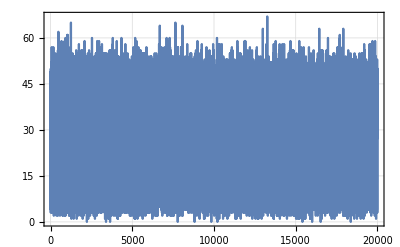
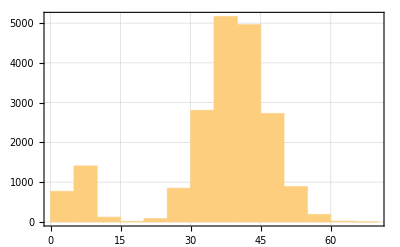
{(9.36027×10^15 | 32. | 9.36027×10^15
9.36027×10^15 | 44. | 9.36027×10^15
9.36027×10^15 | 47. | 9.36027×10^15),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;;;50]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#[[;;;;50]],ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]*)
};
```

## Preprocess

```mathematica
(*threshold counts & convert units*)
datasetProcessed=ThresholdCounts[dataset[[;;,{timeCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ns,1.}];
```

```mathematica
(*subtract initial time*)
datasetProcessed[[;;,1]]-=datasetProcessed[[1,1]];
(*separate out values for convenience*)
dataSampledArr=datasetProcessed[[;;,2]];
tmax=datasetProcessed[[-1,1]]-datasetProcessed[[1,1]];
```

## Process

```mathematica
(*fudge the fit guesses to improve fitting*)
fitGuessFudge={1.000,1.0001,0.0001};
```

```mathematica
(*NonlinearModelFit method*)
fitMethodDJ="Gradient";"ConjugateGradient";"NMinimize";{"Newton","StepControl"->"TrustRegion"};
```

```mathematica
(*number of points to use for fit*)
fitLorentzianNumPoints=10;
```

## FFT!

### Do FFT!

```mathematica
(*guess fmax by averaged sample period*)
numSamplePoints=Length[datasetProcessed];
fmax=1./Mean[datasetProcessed[[2;;,1]]-datasetProcessed[[1;;-2,1]]];
```

```mathematica
(*calculate x-axis for FFT (i.e. freqs)*)
dataFFTFreqs=Range[0,fmax/2.,fmax/(numSamplePoints-1)][[;;IntegerPart[numSamplePoints/2.]]];
```

```mathematica
(*apply FFT to sampled measurements (w/DC subtraction)*)
AbsoluteTiming[
dataFFTFull=Fourier[
dataSampledArr-Mean[dataSampledArr],
FourierParameters->{1,-1}
];
]
```

{0.05262,Null}

### Format FFT Results

```mathematica
(*set correct FFT length*)
dataFFTChop=dataFFTFull[[;;IntegerPart[numSamplePoints/2.]]];
```

```mathematica
dataFFTMag=Transpose[{
dataFFTFreqs,
Abs[dataFFTChop]^2.
}];
```

```mathematica
dataFFTPhase=Transpose[{
dataFFTFreqs,
1./π*Arg[dataFFTChop]
}];
```

## Fit Lorentzian

### Prepare Fit!

```mathematica
(*fit function*)
fitfunc=A*Γ/(Γ^2.+(x-f)^2.);
(*fitfunc=A*Γ/(Γ^2.+(x-f)^2.)+COff;*)
```

```mathematica
(*fit constraints*)
fitConstraintsDJ={
(*A>0.,
Γ>0.*)
};
```

```mathematica
(*guess fit parameters*)
peakIndDJ=Ordering[dataFFTMag[[;;,2]],-1];
ΓGuessDJ=0.5/tmax*Sqrt[2];
fitGuessDJ={
{A,ΓGuessDJ^1.*Subtract@@MinMax[dataFFTMag[[;;,2]]][[-1;;1;;-1]]*fitGuessFudge[[1]]},
{Γ,ΓGuessDJ^1.*fitGuessFudge[[2]]},
{f,First@dataFFTMag[[peakIndDJ,1]]+fmax/(numSamplePoints-1)*fitGuessFudge[[3]]}
}
```

{{A,31257.5},{Γ,0.0000531719},{f,20.0002}}

```mathematica
(*get dataset indices to use for fit*)
(*get points to use for fit*)
If[fitLorentzianNumPoints>=1,

(*true case: use valid PeakFitNumPoints*)
{peakFitIndMin,peakFitIndMax}={
Max[1,peakIndDJ-fitLorentzianNumPoints],
Min[Length[dataFFTMag],peakIndDJ+fitLorentzianNumPoints]
};,

(*false case: use full range*)
{peakFitIndMin,peakFitIndMax}={1,-1};
];
```

```mathematica
(*thy=fitfunc/.{A->fitGuessDJ[[1]],Γ->fitGuessDJ[[2]],f->fitGuessDJ[[3]]}
Show[
{
plotDataFFTMag,
Plot[thy,{x,20,22},PlotRange->Full]
},

PlotRange->{
{20.20,20.25},
(*{Full,Max[dataFFTMag[[;;,2]]]}*)
{Full,Full}
}
]*)
```

### Do & Process Fit

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dataFFTMag[[;;]],
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x,

MaxIterations->Automatic,
(*Method->{"NMinimize"}*)
(*Method->{"Newton","StepControl"->"TrustRegion"}*)
(*Method->"Gradient"(*best for symmetric*)*)
(*Method->"ConjugateGradient"(*best for asymmetric*)*)
Method->fitMethodDJ
];
]
```

{1.1265,Null}

```mathematica
(*format fit params*)
AbsoluteTiming[
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
]
```

{8.48907,Null}

## Plot

## Plot Raw FFT Data

```mathematica
(*plot FFT'd data*)
plotDataFFTMag=ListPlot[
{
dataFFTMag,dataFFTMag
(*fftSampledPeakCallouts*)
},

PlotRange->{
{Full,Full},
(*{Full,Full}*)
{19.98,20.02}
},
PlotRangePadding->False,

FrameLabel->{
 {Style["Power (Ampl^2)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp FFT (RID: "<>ToString[rid]<>")",{Black,Directive[15]}]
}
},

Joined->{
False,True,
False,True
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.011]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.004]},
{DefaultPlotColors[[2]],PointSize[0.011]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.004]}
},

PlotLegends->{
"FFT Data - Ampl^2"
},

ImageSize->Scaled[0.45],
PerformanceGoal->"Speed"
(*MaxPlotPoints->IntegerPart[1.*^4]*)
];
```

## Plot Fitted Lorentzian

### Extra Prep for Plotting Fit

```mathematica
(*add plot points to ensure we plot important parts of lorentzian*)
lorentzianExtraPlotPoints=Range[
Max[(f/.fitRes["BestFitParameters"])-#,
fmax/(numSamplePoints-1)],
Min[(f/.fitRes["BestFitParameters"])+#,
fmax/2.],
fmax/(numSamplePoints-1)*5
]&[fmax/(numSamplePoints-1)*10];
%//Length
```

5

```mathematica
(*adjust plot range to capture only important parts of the lorentzian*)
fitPlotMinF=Max[
(f/.fitRes["BestFitParameters"])-fmax/(numSamplePoints-1)*(numSamplePoints)^0.6,
fmax/(numSamplePoints-1)
]

fitPlotMaxF=Max[
(f/.fitRes["BestFitParameters"])+fmax/(numSamplePoints-1)*(numSamplePoints)^0.6,
fmax/(numSamplePoints-1)
]
```

19.7009

20.2995

### Actual Plot!

```mathematica
(*create an analytical function with only our initial parameter guesses*)
thx=fitfunc/.{A->fitGuessDJ[[1,2]],Γ->fitGuessDJ[[2,2]],f->fitGuessDJ[[3,2]]};
```

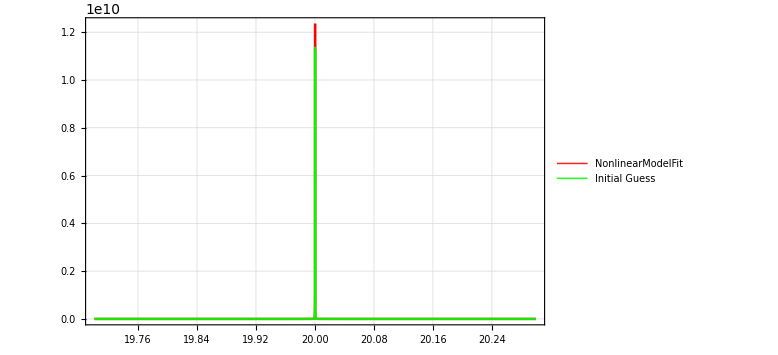

```mathematica
(*plot fitted lorentzian!*)
plotFittedFFTMag=Plot[
{
fitRes[x],
thx
},
{x,fitPlotMinF,fitPlotMaxF},

(*PlotRange->{
{Full,Full},
{Full,Full}
}*)
(*PlotRange->Full,*)
PlotRange->{
{Full,Full},
{Full,Max[dataFFTMag[[;;,2]]]}
},

(*focus plotting around important points*)
PlotPoints->{2000,{(f/.fitRes["BestFitParameters"])}},
(*PlotPoints->{5000,lorentzianExtraPlotPoints},*)

PlotStyle->{
{Red,Thickness[0.003],Opacity[0.88]},
{Green,Thickness[0.003],Opacity[0.88]}
},
PlotLegends->{
"NonlinearModelFit",
"Initial Guess"
},

PerformanceGoal->"Quality"
]
```

## Show

```mathematica
(*fitRes["Properties"]*)
(*fitRes["ParameterTableEntries"]*)
(*fitRes["BestFitParameters"]*)
```

```mathematica
StringForm["Linecenter Precision: `` μHz",NumberForm[Abs[1.*^6*Subtract@@fitRes["ParameterConfidenceIntervals"][[3]]],{∞,3}]]
fitParams
Show[
{
plotDataFFTMag,
plotFittedFFTMag
},

PlotRange->{
{19.9975,20.0025},
(*{Full,Max[dataFFTMag[[;;,2]]]}*)
{Full,Full}
}
]
```

# 2ary: Resolution/Uncertainty vs Samples/Time

```mathematica
(*todo: get Γ and relevant parameter in a single shot - don't run it twice*)
```

todo: document (esp. the block adev part)
Uses datasetProcessed (from import & regular process section).
Note: obviously requires “Import & Regular Process” to be run.

```mathematica
(*create x-axis array of # of points to use for FFT*)
sampleLengthArrX=Join[
Range[100,1000,50],
Range[1000,10000,500],
Range[10000,100000,2000],
Range[100000,1000000,20000]
]//IntegerPart//DeleteDuplicates//Sort;
lengthArrInitial=Length[sampleLengthArrX];
```

```mathematica
(*throw away bad fits etc. based on whether they fit the correct peak freq guess seed within some tolerance*)
{peakFreqValue,peakFreqTolerance}={20.0002,1};
```

```mathematica
(*sample period used to calculate fisher information*)
fisherInfTperiod=13.3*ms;
(*displacement used for the measurements; used to calculate the fisher info limit*)
fisherInfα=0.4;
```

```mathematica
(*number of points to use for peak fitting (used by both single style and ADEV style)*)
numPointsPeakFitScalingADEV=-1;
```

```mathematica
(*select whether precision or error: can be "ERR" or "95CI"*)
precisionProcStyle="ERR";
```

```mathematica
(*tune fitting values*)
fitMethodScalingProcess="Gradient";
fitFudgeScalingProcess={0.8,1.5,0.00};
```

## Process

```mathematica
(*keep only N nums below our actual sample length*)
sampleLengthArrX=Select[sampleLengthArrX,#<Length[datasetProcessed]/1.&];
Print[StringForm["Start: `` => Valid: ``",lengthArrInitial,Length[sampleLengthArrX]]];
```

Start: 127 => Valid: 126

```mathematica
(*convert indices/# of points to total measurement time*)
sampleTimeArrX=datasetProcessed[[sampleLengthArrX,1]];
```

## Batch Process Raw Data - Single Style

### Run & Cherry Pick

```mathematica
(*process constituent FFTs*)
AbsoluteTiming[
batchProcDataRes=ParallelMap[
FFTBlockFit[
datasetProcessed[[;;#]],
"PeakFitNumPoints"->numPointsPeakFitScalingADEV,
"FitMethod"->fitMethodScalingProcess,
"FitFudgeArray"->fitFudgeScalingProcess
]&,
sampleLengthArrX[[;;]]
];
]
```

NonlinearModelFit::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{44.3899,Null}

```mathematica
(*select only fit results which successfully fit our target peak within a given tolerance*)
validBatchFitIndices=First/@Position[
batchProcDataRes,
n_List/;Abs[(f/.n[[3]]["BestFitParameters"])-peakFreqValue]<peakFreqTolerance,
(*_List?(Abs[(f/.#[[3]]["BestFitParameters"])-peakFreqValue]<peakFreqTolerance&),*)
{1}
];
```

```mathematica
(*tmp remove*)
validBatchFitIndices=validBatchFitIndices[[2;;]];
```

```mathematica
(*cherry pick only the runs with good fits*)
sampleLengthArrXCherryPicked=sampleLengthArrX[[validBatchFitIndices]];
sampleTimeArrXCherryPicked=sampleTimeArrX[[validBatchFitIndices]];
batchProcDataResCherryPicked=batchProcDataRes[[validBatchFitIndices]];
```

```mathematica
(*take only the lorentzian fit results*)
ADEVFitRes=batchProcDataResCherryPicked[[;;,3]];
```

### Extract Target Results

```mathematica
(*precision: extract confidence intervals from fit results for plotting*)
AbsoluteTiming[
If[precisionProcStyle=="ERR",

(*case: error style*)
precisionADEVData=ParallelMap[
#["ParameterTableEntries"][[3,2]]&,
ADEVFitRes
];,

(*case: 95% confint style*)
precisionADEVData=ParallelMap[
#["ParameterConfidenceIntervals"][[3]]&,
ADEVFitRes
];
precisionADEVData=Abs[Subtract@@@precisionADEVData];
]
]
```

{271.019,Null}

```mathematica
(*format precisions for plotting*)
precisionADEVData=Transpose[{
sampleTimeArrXCherryPicked,
precisionADEVData}
];
```

```mathematica
(*resolution: extract fitted parameter from fit results for plotting*)
AbsoluteTiming[
resolutionADEVData=ParallelMap[
Γ/.#["BestFitParameters"]&,
ADEVFitRes
];

(*format resolutions for plotting*)
resolutionADEVData=Transpose[{
sampleTimeArrXCherryPicked,
resolutionADEVData
}];
]
```

{219.142,Null}

```mathematica
(*create extra values to be compatible with ADEV-style processing*)
precADEVDataPlot=MapThread[
{#1[[1]],Around[#1[[2]],#2[[2]]]}&,
{precisionADEVData,
Transpose[{precisionADEVData[[;;,1]],ConstantArray[1.*^-9,Length[precisionADEVData]]}]}
];
resADEVDataPlot=MapThread[
{#1[[1]],Around[#1[[2]],#2[[2]]]}&,
{resolutionADEVData,
Transpose[{resolutionADEVData[[;;,1]],ConstantArray[1.*^-9,Length[resolutionADEVData]]}]}
];
```

## Batch Process Raw Data - ADEV Style

### ADEV Split Block Proc Func

```mathematica
(*todo: document*)
Clear[OverlapBlockProcess];
OverlapBlockProcess[
dataset_List,
blockSize:(_Integer|_Real),
peakFreq_:(_Integer|_Real),
peakTol:(_Integer|_Real)
]:=Module[
{
(*partition dataset into non-overlapping blocks*)
dsBlocks=Partition[dataset,blockSize],
procRes,validProcRes,precisionADEVData,resolutionADEVData
},

(*process all non-overlapping blocks*)
procRes=Map[
FFTBlockFit[
#,
"FitMethod"->fitMethodScalingProcess,
"PeakFitNumPoints"->numPointsPeakFitScalingADEV,
"FitFudgeArray"->fitFudgeScalingProcess
]&,
dsBlocks
];

(*select only results which fit OK*)
validProcRes=Select[
procRes,
Abs[(f/.#[[3]]["BestFitParameters"])-peakFreq]<peakTol&
];
(*Print[StringForm["Block Size: ``\tStart: `` => Valid: ``",blockSize,Length[procRes],Length[validProcRes]]];*)

(*precision: extract confidence intervals from fit results for plotting*)
(*precisionADEVData=Map[
#["ParameterConfidenceIntervals"][[3]]&,
validProcRes[[;;,3]]
];
precisionADEVData=Subtract@@@precisionADEVData;*)
(*precision: take as uncertainty of linecenter*)
If[precisionProcStyle=="ERR",

(*case: error style*)
precisionADEVData=Map[
#["ParameterTableEntries"][[3,2]]&,
validProcRes[[;;,3]]
];,

(*case: 95% confint style*)
precisionADEVData=Map[
#["ParameterConfidenceIntervals"][[3]]&,
validProcRes[[;;,3]]
];
precisionADEVData=Subtract@@@precisionADEVData;
];

(*extract precision & resolution data*)
resolutionADEVData=Map[
Γ/.#["BestFitParameters"]&,
validProcRes[[;;,3]]
];

(*clean up after ourselves*)
Clear[procRes,dsBlocks,validProcRes];ClearInOut[];ClearSystemCache[];

Return[{
(*need to ensure results are positive otherwise booboo*)
Abs[precisionADEVData],
Abs[resolutionADEVData]
}];

];
```

### Run ADEV Style

```mathematica
(*calculate!*)
AbsoluteTiming[
resADEVScaling=ParallelMap[
OverlapBlockProcess[
datasetProcessed,
#,
peakFreqValue,peakFreqTolerance
]&,
sampleLengthArrX
];
]
```

{132.706,Null}

#### Cherry Pick “Valid” Results Only

```mathematica
(*select only processed results which haven't returned an empty list*)
validBatchFitIndices=First/@Position[
resADEVScaling,
n_List/;Length[n[[1]]]>0&&Length[n[[2]]]>0,
{1}
]

(*todo: make this a print instead*)
Length/@{sampleLengthArrX,validBatchFitIndices};
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
(*cherry pick only the runs with good fits*)
sampleLengthArrXCherryPicked=sampleLengthArrX[[validBatchFitIndices]];
sampleTimeArrXCherryPicked=sampleTimeArrX[[validBatchFitIndices]];
resADEVScalingCherryPicked=resADEVScaling[[validBatchFitIndices]];
```

```mathematica
(*tmp remove*)
{minIDXCherryPick,maxIDXCherryPick}={10,-1};
sampleTimeArrXCherryPicked=sampleTimeArrXCherryPicked[[minIDXCherryPick;;maxIDXCherryPick]];
resADEVScalingCherryPicked=resADEVScalingCherryPicked[[minIDXCherryPick;;maxIDXCherryPick]];
resADEVScalingCherryPicked//Dimensions
```

### Extract Target Results

#### Precision

```mathematica
(*format precisions for plotting*)
precisionADEVData=Transpose[{
sampleTimeArrXCherryPicked,
Mean/@resADEVScalingCherryPicked[[;;,1]]
}];
```

```mathematica
(*calculate errors for later around/fit*)
precisionADEVErrs=Transpose[{
sampleTimeArrXCherryPicked,
StandardDeviation[#]/Sqrt[Length[#]]&/@resADEVScalingCherryPicked[[;;,1]]
}];
```

```mathematica
(*add uncertainty to data points*)
precADEVDataPlot=MapThread[
{#1[[1]],Around[#1[[2]],#2[[2]]]}&,
{precisionADEVData,
precisionADEVErrs}
];
```

#### Resolution

```mathematica
(*format resolutions for plotting*)
resolutionADEVData=Transpose[{
sampleTimeArrXCherryPicked,
Mean/@resADEVScalingCherryPicked[[;;,2]]
}];
```

```mathematica
(*calculate errors for later around/fit*)
resolutionADEVErrs=Transpose[{
sampleTimeArrXCherryPicked,
StandardDeviation[#]/Sqrt[Length[#]]&/@resADEVScalingCherryPicked[[;;,2]]
}];
```

```mathematica
(*add uncertainty to data points*)
resADEVDataPlot =MapThread[
   {#1[[1]], Around[#1[[2]], #2[[2]]]} &,
   {resolutionADEVData,
    resolutionADEVErrs}
   ];
```

## Fit Trends

### Fitting w/ Around[]

```mathematica
(*fit Around data for log-log'd linear model*)
Clear[FitLinearFuncLog];
FitLinearFuncLog[dataset_List]:=Block[{x},
Module[
{
dataRaw=Log[dataset],
dataValues,dataWeights
},

(*separate data values from uncertainties*)
dataValues={#[[1]],#[[2]]["Value"]}&/@dataRaw;
(*dataWeights=(#[[2]]["Uncertainty"]&/@dataRaw)^-2.;*)

(*scale weights for log-log fit*)
dataWeights=(
1.+(#[[2]]["Uncertainty"]&/@dataRaw)/dataValues[[;;,2]]
)^-2.;

Return[
LinearModelFit[
dataValues,
{x},
x,

Weights->dataWeights
]
];
];
];
```

### Linear Fit

```mathematica
(*do linear fits to log'd data*)
(*linearADEVFitRes=FitLinearFunc/@{precisionADEVData,resolutionADEVData};*)
linearADEVFitRes=FitLinearFuncLog/@{precADEVDataPlot,resADEVDataPlot};
```

```mathematica
(*get fit parameters*)
linearADEVFitParams=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@linearADEVFitRes;
```

### Power-Law Fit

```mathematica
(*do power fits to normal data*)
powerADEVFitRes=FitPowerFunc/@{precisionADEVData,resolutionADEVData};
```

```mathematica
(*get fit parameters*)
powerADEVFitParams=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@powerADEVFitRes;
```

## Plot Results

## Plot Data

### Plot Precision

```mathematica
(*plot frequency precision vs time*)
precisionADEVDataPlot=ListLogLogPlot[
{
precADEVDataPlot,
precisionADEVData
},

PlotRange->{
{Full,Full},
{Full,Full}
},

(*plot formatting*)
PlotRangePadding->False,
FrameTicksStyle->Directive[Black,20],
FrameLabel->{ 
{Style["Confidence Interval (95%, Hz)",{Black,Directive[15]}],None},
{
Style["Total Measurement Time (s)",{Black,Directive[15]}],
Style[StringForm["Parameter Scaling vs Total Measurement Time\nRID: ``",rid],{Black,Directive[15]}]
}
},

(*labelling*)
PlotLabels->Placed[
{
Style["PRECISION",{DefaultPlotColors[[1]],Directive[15]}],
None
},
{{Scaled[0.7],Before}}
],
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.011]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.004]}
},

(*size output image*)
Joined->{True,False},
AspectRatio->Full,
ImageSize->{800,500}
];
```

### Plot Resolution

```mathematica
(*plot resolution/linewidth vs time*)
resolutionADEVDataPlot=ListLogLogPlot[
{
resADEVDataPlot,
resolutionADEVData(*resolution*)
},

PlotRange->{
{Full,Full},
{Full,Full}
},

(*plot formatting*)
PlotRangePadding->False,
FrameTicksStyle->Directive[Black,20],
FrameLabel->{ 
{Style["Resolution (Γ, Hz)",{Black,Directive[15]}],None},
{
Style["Total Measurement Time (s)",{Black,Directive[15]}],
Style[StringForm["Parameter Scaling vs Total Measurement Time\nRID: ``",rid],{Black,Directive[15]}]
}
},

(*labelling*)
PlotLabels->Placed[
{
Style["RESOLUTION",{DefaultPlotColors[[2]],Directive[15]}],
None
},
{{Scaled[0.7],Before}}
],
PlotStyle->{
{DefaultPlotColors[[2]],PointSize[0.011]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.004]}
},

(*size output image*)
Joined->{True,False},
AspectRatio->Full,
ImageSize->{800,500}
];
```

## Plot ADEV Scaling Fits

### Linear

```mathematica
(*plot linear fit result - precision*)
linearPrecisionADEVFitPlot=LogLogPlot[
Exp[#[Log[x]]],
{x,Exp[#["Data"][[1,1]]],Exp[#["Data"][[-1,1]]]},

FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.004]}
}
]&[linearADEVFitRes[[1]]];
```

```mathematica
(*plot linear fit result - resolution*)
linearResolutionADEVFitPlot=LogLogPlot[
Exp[#[Log[x]]],
{x,Exp[#["Data"][[1,1]]],Exp[#["Data"][[-1,1]]]},

FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[2]],Thickness[0.004]}
}
]&[linearADEVFitRes[[2]]];
```

### Power-Law

```mathematica
(*plot power-law fit results - precision*)
powerADEVFitPlot=LogLogPlot[
#[x],
{x,#["Data"][[1,1]],#["Data"][[-1,1]]},
FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[2]],Thickness[0.004]}
}
]&/@powerADEVFitRes;
```

```mathematica
(*plot power-law fit results - precision*)
powerPrecisionADEVFitPlot=LogLogPlot[
#[x],
{x,#["Data"][[1,1]],#["Data"][[-1,1]]},
FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.004]}
}
]&[powerADEVFitRes[[1]]];
```

```mathematica
(*plot power-law fit results - resolution*)
powerResolutionADEVFitPlot=LogLogPlot[
#[x],
{x,#["Data"][[1,1]],#["Data"][[-1,1]]},
FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[2]],Thickness[0.004]}
}
]&[powerADEVFitRes[[2]]];
```

## Fisher Information/SQL

```mathematica
(*create fisher info function*)
Clear[PrecisionFisherInfo];
PrecisionFisherInfo[α_,Tperiod_,Tfinal_,fockN_:0]:=(
(4.*(2.*fockN+1.))
*(1./6.*α^2*Tfinal^3/Tperiod)
(*1/(0.209*Tperiod^3)
*(α^2*(250*μs)^2*Tfinal^3)*)
)^-0.5;
```

```mathematica
(*plot linear fit result - precision*)
fisherInfoADEVFitPlot=LogLogPlot[

PrecisionFisherInfo[fisherInfα,fisherInfTperiod,T,0],
{T,Exp[#["Data"][[1,1]]],Exp[#["Data"][[-1,1]]]},

FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["ADEVs\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.006],Dashed,Dashing[0.04]}
},

PlotLegends->{
"SQL - Precision"
}
]&[linearADEVFitRes[[1]]];
```

## Show

```mathematica
sc0=fisherInfoADEVFitPlot;
```

{ | Estimate | Standard Error | Confidence Interval
1 | 0.992682 | 0.184932 | {0.626115,1.35925}
x | -1.84016 | 0.0258374 | {-1.89137,-1.78894}, | Estimate | Standard Error | Confidence Interval
1 | -1.00277 | 0.210405 | {-1.41983,-0.585713}
x | -0.989133 | 0.0293985 | {-1.04741,-0.93086}}

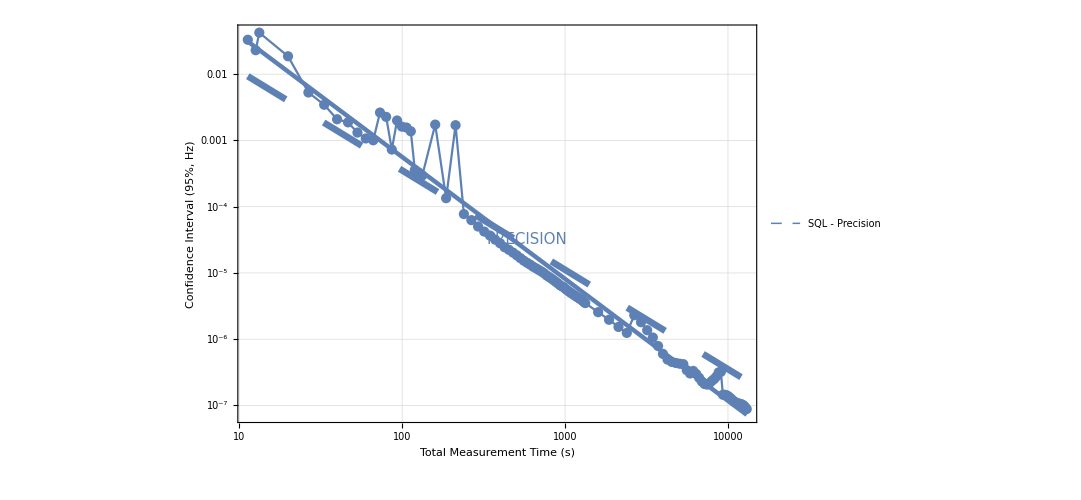

```mathematica
{
linearADEVFitParams[[1]],
linearADEVFitParams[[2]]
}
Show[
{
precisionADEVDataPlot,
(*resolutionADEVDataPlot,*)
(*linearResolutionADEVFitPlot,*)
(*sca,sca2,sca3,*)
linearPrecisionADEVFitPlot,
fisherInfoADEVFitPlot
},

PlotRange->{
{Full,Full},
{Automatic,Automatic}
}]
```

## Show - RDX

```mathematica
precN0FitParams=linearADEVFitParams[[1]];
precN0DataPlot=precisionADEVDataPlot;
precN0FitPlot=linearPrecisionADEVFitPlot;
```

```mathematica
{precN0FitParams,precN1FitParams}
```

{ | Estimate | Standard Error | Confidence Interval
1 | 5.53879 | 0.459635 | {4.61906,6.45852}
x | -2.05324 | 0.0714736 | {-2.19626,-1.91023}, | Estimate | Standard Error | Confidence Interval
1 | 4.73842 | 0.277873 | {4.18393,5.2929}
x | -2.09651 | 0.0452454 | {-2.18679,-2.00622}}

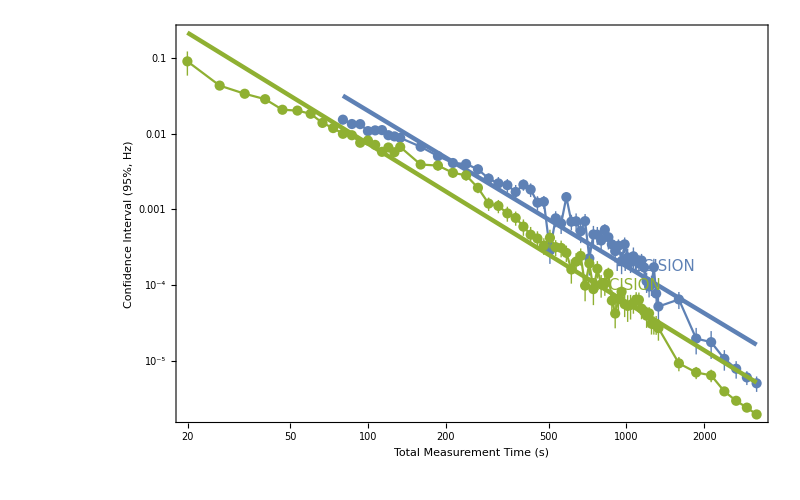

```mathematica
Show[
{
precN0DataPlot,precN0FitPlot,
precN1DataPlot,precN1FitPlot
},

PlotRange->{
{Full,Full},
{Full,Full}
}]
```

## Save Data

```mathematica
tmpPrecisionData={#[[1]],#[[2]]["Value"],#[[2]]["Uncertainty"]}&/@precADEVDataPlot;
tmpResolutionData={#[[1]],#[[2]]["Value"],#[[2]]["Uncertainty"]}&/@resADEVDataPlot;
```

```mathematica
Export[FileNameJoin[{"C:\\Users\\EGGS2\\Documents\\Correlation Sampling",ToString[StringForm["adev_proc_``_precision.csv",rid]]}],tmpPrecisionData,OverwriteTarget->False];
Export[FileNameJoin[{"C:\\Users\\EGGS2\\Documents\\Correlation Sampling",ToString[StringForm["adev_proc_``_resolution.csv",rid]]}],tmpResolutionData,OverwriteTarget->False];
```

## Inspect

```mathematica
(*(*quick test*)
FFTBlockPlotNicer[
datasetProcessed[[;;#]],
"FitMethod"->"ConjugateGradient",
"FitFudgeArray"->{1.1,1.1,0.},
"PeakFitNumPoints"->numPointsPeakFitScalingADEV
]&[sampleLengthArrX[[-1]]]*)
```

```mathematica
(*fdj it b/c lazy lol*)
AbsoluteTiming[
inspectScalingDatasets=ParallelMap[
{
#,
FFTBlockPlotNicer[
datasetProcessed[[;;#]],

"FitMethod"->"Gradient",
"FitFudgeArray"->{0.9,1.5,0.0001},
"PeakFitNumPoints"->50
]
}&,

sampleLengthArrXCherryPicked[[;;;;2]]
];
]
(*reformat for plotting*)
inspectScalingDatasets=Join[{#[[1]]},#[[2]]]&/@inspectScalingDatasets;
(*convert sample num to times*)
inspectScalingDatasets[[;;,1]]*=1./fmax;
```

NonlinearModelFit::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{19.1245,Null}

{9,4}

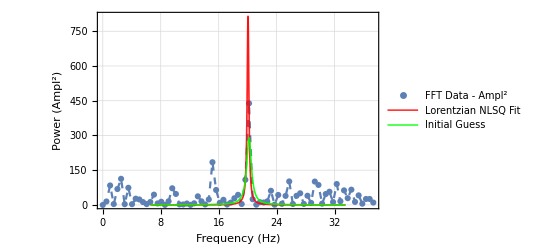
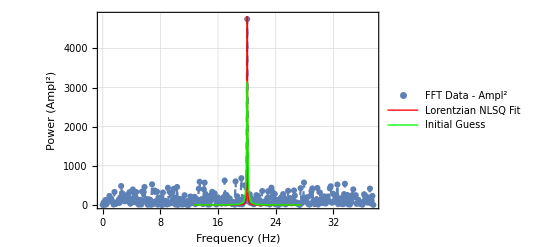
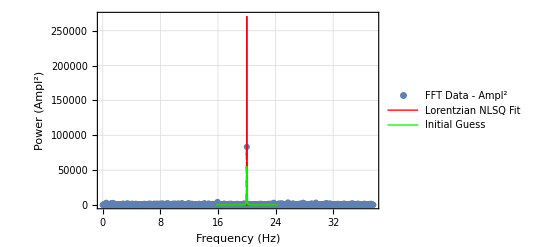
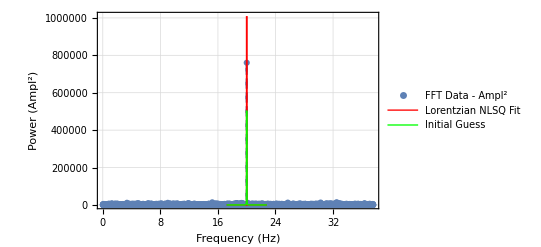
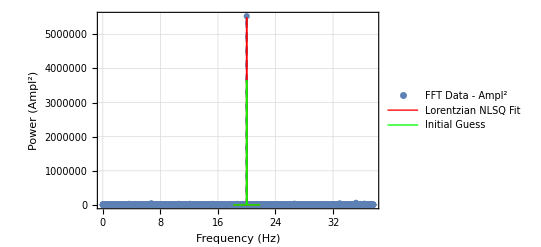
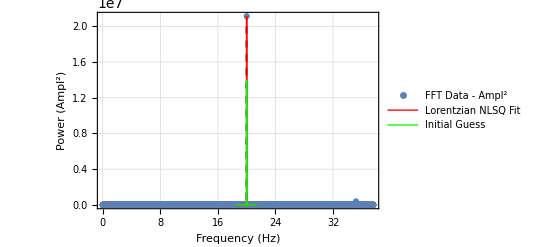
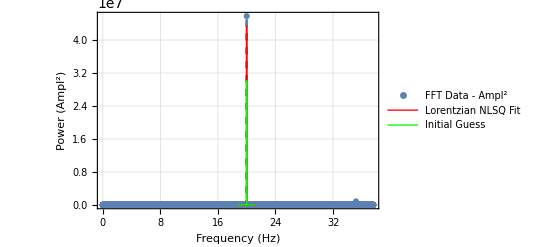
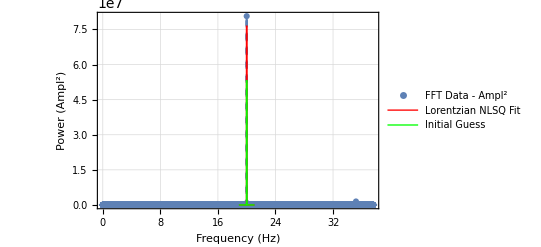
{(1.99498
Linecenter Precision: 453437.533 μHz
 | Estimate | Standard Error | Confidence Interval
A | 17.4078 | 14.9776 | {-12.4494,47.2651}
Γ | 0.146126 | 0.212903 | {-0.278288,0.570539}
f | 20.0494 | 0.113731 | {19.8227,20.2762}
-Graphics-),(8.6449
Linecenter Precision: 106283.082 μHz
 | Estimate | Standard Error | Confidence Interval
A | 4.75676 | 2.16248 | {0.492302,9.02121}
Γ | 0.0313947 | 0.00859981 | {0.0144357,0.0483536}
f | 20.0467 | 0.0269478 | {19.9935,20.0998}
-Graphics-),(33.2496
Linecenter Precision: 34679.339 μHz
 | Estimate | Standard Error | Confidence Interval
A | 0.718606 | 0.444082 | {-0.157132,1.59434}
Γ | 0.00162698 | 0.0140048 | {-0.0259907,0.0292447}
f | 20.0107 | 0.00879286 | {19.9933,20.028}
-Graphics-),(99.7488
Linecenter Precision: 13738.683 μHz
 | Estimate | Standard Error | Confidence Interval
A | 0.257429 | 0.175434 | {-0.0885292,0.603387}
Γ | 0.000503066 | 0.00207609 | {-0.00359102,0.00459715}
f | 20.0026 | 0.00348341 | {19.9957,20.0095}
-Graphics-),(265.997
Linecenter Precision: 1781.260 μHz
 | Estimate | Standard Error | Confidence Interval
A | 0.246202 | 0.0573635 | {0.13308,0.359323}
Γ | 0.000209625 | 0.0000580278 | {0.0000951928,0.000324057}
f | 20.0012 | 0.000451634 | {20.0003,20.0021}
-Graphics-),(531.994
Linecenter Precision: 354.983 μHz
 | Estimate | Standard Error | Confidence Interval
A | 0.318941 | 0.0296572 | {0.260456,0.377425}
Γ | 0.000120804 | 0.0000178932 | {0.0000855178,0.000156089}
f | 20.0007 | 0.0000900049 | {20.0005,20.0009}
-Graphics-),(797.99
Linecenter Precision: 256.593 μHz
 | Estimate | Standard Error | Confidence Interval
A | 28.7693 | 2.76457 | {23.3175,34.2211}
Γ | 0.000813262 | 0.0000424809 | {0.000729488,0.000897035}
f | 20.0006 | 0.0000650585 | {20.0004,20.0007}
-Graphics-),(1063.99
Linecenter Precision: 190.165 μHz
 | Estimate | Standard Error | Confidence Interval
A | 28.5176 | 2.70802 | {23.1774,33.8579}
Γ | 0.000609731 | 0.0000314708 | {0.00054767,0.000671792}
f | 20.0005 | 0.0000482159 | {20.0004,20.0006}
-Graphics-),(1329.98
Linecenter Precision: 29.681 μHz
 | Estimate | Standard Error | Confidence Interval
A | 0.978448 | 0.019038 | {0.940905,1.01599}
Γ | 0.0000883494 | 1.45117×10^-6 | {0.0000854877,0.0000912112}
f | 20.0005 | 7.52566×10^-6 | {20.0004,20.0005}
-Graphics-)}

```mathematica
(*batch show*)
inspectScalingDatasets//Dimensions
MatrixForm/@inspectScalingDatasets
```

# 2ary: SNR Longterm Stability Process

todo: document
Uses datasetProcessed (from import & regular process section).
Note: obviously requires “Import & Regular Process” to be run (but only up until before “Process”)

```mathematica
blockSizeSamples=5000;
Length[datasetProcessed]/blockSizeSamples//IntegerPart
```

200

## Process

## Processing Functions

```mathematica
(*process statistics on FFT*)
Clear[FFTStatsProcess];
FFTStatsProcess[dataFFT_List]:=Module[
{
bgrPoints=dataFFT[[;;,2]],
bgrThreshold=Mean[dataFFT[[;;,2]]]+StandardDeviation[dataFFT[[;;,2]]]*5.,

bgrPointsReduced,bgrDistFit,
bgrHistBinSize,bgrHistPlot,bgrDistFitPlot
},


(*remove peak points to make hist happier*)
(*note: exclude 0 points b/c it makes EstimatedDistribution unhappy*)
bgrPointsReduced=Select[bgrPoints,1.*^-9<#<bgrThreshold&];

(*fit FFT background to a Gamma (i.e. Γ(α, λ)) distribution*)
bgrDistFit=EstimatedDistribution[bgrPointsReduced,GammaDistribution[α,λ]];
(*get histogram bin size from HistogramList lol*)
bgrHistBinSize=Mean[#[[2;;-1]]-#[[1;;-2]]]&[HistogramList[bgrPointsReduced,"Scott","Probability"][[1]]];

(*plot data histogram*)
bgrHistPlot=Histogram[
bgrPointsReduced,
"Scott",
"Probability",

FrameLabel->{
 {Style["Probability",{Black,Directive[15]}],None},
{
Style["Power (Ampl^2)",{Black,Directive[15]}],
Style[StringForm["FFT Background Statistics: N = ``\nRID: ``",numSamplePoints,rid],{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
];

(*plot fitted distribution*)
bgrDistFitPlot=Plot[
bgrHistBinSize*PDF[bgrDistFit,x],
{x,#1,#2},

ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
]&[
(*x_min for plotting distribution*)
Max[0.,Mean[bgrDistFit]-4.*StandardDeviation[bgrDistFit]],

(*x_max for plotting distribution*)
Mean[bgrDistFit]+4.*StandardDeviation[bgrDistFit]
];


Return[
<|
"Max"->Max[dataFFT[[;;,2]]],
"BackgroundDistribution"->bgrDistFit,
"StatisticsRaw"->{Mean[#],StandardDeviation[#]}&[bgrPoints],
"StatisticsBackgroundReduced"->{Mean[#],StandardDeviation[#]}&[bgrPointsReduced],
"StatisticsBackgroundDistribution"->{Mean[#],StandardDeviation[#]}&[bgrDistFit],
"Figure"->Show[{bgrHistPlot,bgrDistFitPlot},PlotRange->Automatic,ImageSize->{800,500},AspectRatio->Full]
|>
];
];
```

## Batch Process Raw Data

```mathematica
(*partition data into blocks of size blockSizeSamples*)
datasetChopped=Partition[datasetProcessed,blockSizeSamples];
datasetChoppedTimes=First/@datasetChopped[[;;,;;,1]];
```

```mathematica
(*process constituent FFTs and get full set of results*)
AbsoluteTiming[
batchProcDataRes=ParallelMap[
FFTBlockFit[#]&,
datasetChopped
];
]
```

{20.4424,Null}

```mathematica
(*conduct FFT statistics*)
AbsoluteTiming[
batchProcDataFFTStats=ParallelMap[
FFTStatsProcess,
batchProcDataRes[[;;,1]]
];
]
```

{11.3164,Null}

## Extract Results

```mathematica
(*extract SNR from raw FFT peak and mean of dist-fitted bgr*)
datasetChoppedSignal=Transpose[{
datasetChoppedTimes,
#["Max"]&/@batchProcDataFFTStats
}];
```

```mathematica
datasetChoppedBackground=Transpose[{
datasetChoppedTimes,
#["StatisticsBackgroundDistribution"][[1]]&/@batchProcDataFFTStats
}];
```

```mathematica
datasetChoppedSNR=Transpose[{
datasetChoppedTimes,
(#["Max"]/#["StatisticsBackgroundDistribution"][[1]])&/@batchProcDataFFTStats
}];
```

```mathematica
(*process dark state probability vs time*)
(*extract time-series stats - dark-state probability*)
(*datasetChoppedPDark=batchProcDataPDark={Mean[#[[;;,2]]],StandardDeviation[#[[;;,2]]]/(√Length[#[[;;,2]]])}&/@datasetChopped;*)
datasetChoppedPDark=Transpose[{
datasetChoppedTimes,
Mean[#[[;;,2]]]&/@datasetChopped
}];
```

## Plot Results

```mathematica
(*plot amplitude stability data*)
amplitudeStabilityPlots=MapThread[
(*plot function*)
PlotTMP[
<|
#2->#1
|>,
"Time (s)",
#3,
ToString[StringForm["Amplitude Stability vs Time - RIDs: ``",rid]]
]&,

(*relevant datasets*)
{
{datasetChoppedSignal,datasetChoppedBackground,datasetChoppedSNR,datasetChoppedPDark},
{"Signal","Background","SNR","P_Dark"},
{"Peak Amplitude","Background (Mean)","SNR","Dark-State Probability (P_Dark)"}
}
];
```

## Show

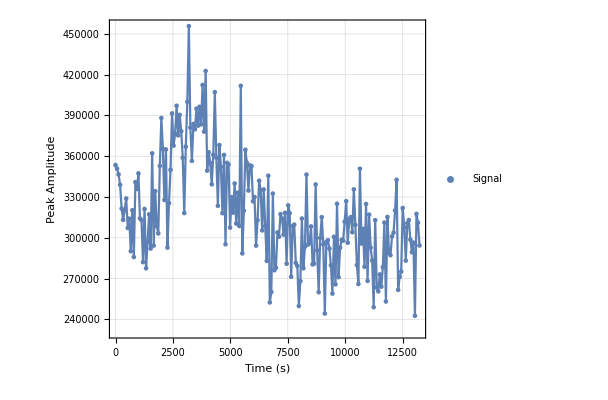
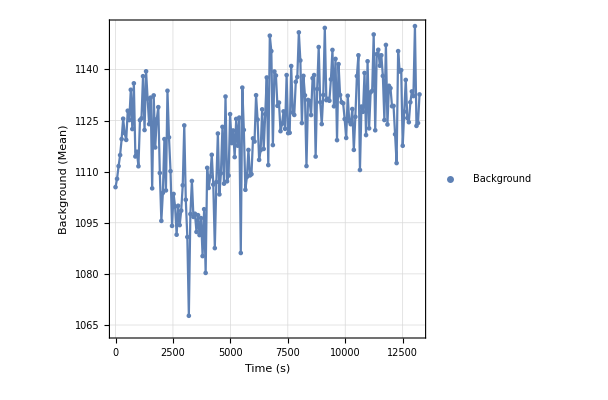
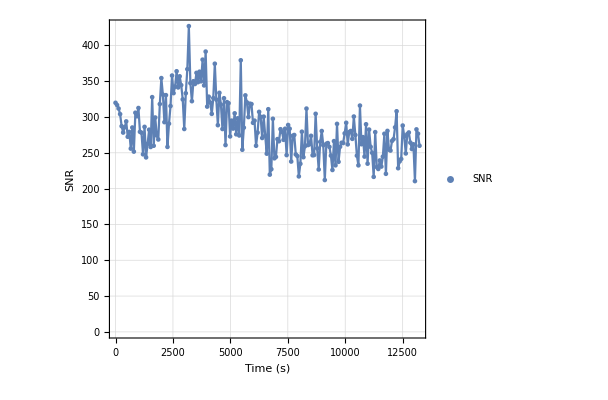
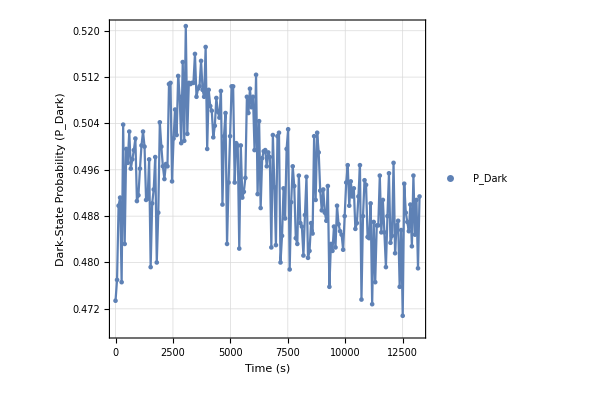

```mathematica
(*show all relevant figures*)
Show[
{#},
ImageSize->{450,400}
]&/@amplitudeStabilityPlots
```

## Inspect

```mathematica
(*(*fdj it*)
AbsoluteTiming[
inspectChoppedDatasets=ParallelMap[
FFTBlockPlotNicer,
datasetChopped[[;;]]
];
]*)
```

```mathematica
(*(*batch show*)
MatrixForm/@inspectChoppedDatasets*)
```

# Aux: Secular Frequency Stability/Drift

## Data Store

```mathematica
(*2025/07/16*)
wsecString20250716="
• 1859PM:702.646 kHz
• 1904PM:702.663 kHz
• 1912PM:702.692 kHz
• 1918PM:702.727 kHz
• 1922PM:702.685 kHz
• 1932PM:702.719 kHz
• 1938PM:702.724 kHz
• 1944PM:702.731 kHz
• 1950PM:702.736 kHz
• 1957PM:702.742 kHz
• 2004PM:702.746 kHz
• 2012PM:702.753 kHz
• 2020PM:702.754 kHz
• 2028PM:702.759 kHz
• 2036PM:702.758 kHz
• 2052PM:702.752 kHz
• 2342PM:702.768 kHz
• 2359PM:702.768 kHz
• 0031AM:702.784 kHz
• 0046AM:702.776 kHz
• 0135AM:702.786 kHz
";
```

```mathematica
(*2025/09/19*)
wsecString20250919="
• 2037PM:700.513 kHz
• 2049PM:700.624 kHz
• 2100PM:700.635 kHz
• 2100PM:700.635 kHz
• 2200PM:700.612 kHz
• 2221PM:700.617 kHz
• 2230PM:700.603 kHz
• 0004AM:700.585 kHz
• 0013AM:700.580 kHz
• 0037AM:700.578 kHz
• 0131AM:700.596 kHz
• 0139AM:700.575 kHz
• 0203AM:700.570 kHz
• 0214AM:700.580 kHz
";
```

## Regex Extract & Process

```mathematica
(*select data from storage*)
wsecStringDJ=wsecString20250716;
dateDJ={2025,07,16};
```

```mathematica
(*extract details using StringCases + regex*)
valProc=StringCases[
(*string to be processed*)
wsecStringDJ,

(*regex*)
RegularExpression[
".*(\d{2}(?=(\d{2})[AP])).*(A|P).*:\s*(\d*\.\d*).*kHz"
]->

(*process regex capture groups*)
{
"$1","$2","$3","$4"
}
]
Length[%]
```

Syntax::sntoct2: 2 hexadecimal digits are required after \. to construct an 8-bit character.

{{18,59,P,702.646},{19,04,P,702.663},{19,12,P,702.692},{19,18,P,702.727},{19,22,P,702.685},{19,32,P,702.719},{19,38,P,702.724},{19,44,P,702.731},{19,50,P,702.736},{19,57,P,702.742},{20,04,P,702.746},{20,12,P,702.753},{20,20,P,702.754},{20,28,P,702.759},{20,36,P,702.758},{20,52,P,702.752},{23,42,P,702.768},{23,59,P,702.768},{00,31,A,702.784},{00,46,A,702.776},{01,35,A,702.786}}

21

```mathematica
(*process regex results into values*)
valProc[[;;,{1,2,4}]]=ToExpression[valProc[[;;,{1,2,4}]]];
(*convert into date objects*)
dateVals=DateObject[Join[dateDJ,#]]&/@valProc[[;;,{1,2}]];
(*add 24 hours when we cross over*)
dateVals=MapThread[
DatePlus[#1,#2]&,
{
dateVals,
valProc[[;;,3]]/.{"P"->0,"A"->1}
}
];
```

## Plot

```mathematica
(*format data for time series plot*)
wsecDriftTimeSeriesData=Transpose[{dateVals,valProc[[;;,4]]}];
(*extract and subtract mean to expand y-axis*)
wsecDriftMeankHz=Mean[wsecDriftTimeSeriesData[[;;,2]]];
wsecDriftTimeSeriesData[[;;,2]]=(wsecDriftTimeSeriesData[[;;,2]]-wsecDriftMeankHz)*1.*^3;
```

```mathematica
(*plot wsec drift as time series*)
wsecDriftTimeSeriesPlot=DateListPlot[
{
wsecDriftTimeSeriesData,
wsecDriftTimeSeriesData
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Frequency Drift (Hz)",{Black,Directive[15]}],None},
{
Style["Time",{Black,Directive[15]}],
Style["Secular Frequency Drift\nMean Freq (kHz): "<>ToString[NumberForm[wsecDriftMeankHz,{∞,3}]],{Black,Directive[15]}]
}
},

Joined->{False,True},
ImageSize->Scaled[0.4]
];
```

## Show

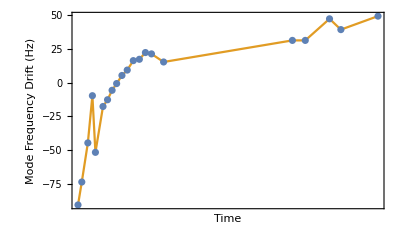

```mathematica
wsecDriftTimeSeriesPlot
```

# 2ary: Precision vs # of FFT Points Used for Fit (Deprecated)

Fits subsets of the FFT’d data centered around the peak to see how precision changes with # of FFT points used for the Lorentzian fit.
Uses dataFFTMag (from import & regular process section).
Note: obviously requires “Import & Regular Process” to be run.

```mathematica
(*create x-axis array of # of points to scan*)
pointsArrX=Join[
Range[2,10],
Range[10,250,5],
Range[200,1000,25]
]//IntegerPart//DeleteDuplicates//Sort;
Length[pointsArrX]

(*keep only N nums below our actual sample length*)
pointsArrX=Select[
pointsArrX,
#<Length[datasetProcessed]/2.&
];
Length[pointsArrX]
```

87

87

## Process

## Processing Function

```mathematica
(*create func to fit lorentzian to subranges of known dataset*)
Clear[FitSubsetFunc];
FitSubsetFunc[subRange_]:=With[
{
dataFFTFitTMP=dataFFTMag[[
Max[1,peakIndDJ-subRange];;
Min[Length[dataFFTMag],peakIndDJ+subRange]
]]
},

Return[
{
(*x-axis value: # of points*)
Length[dataFFTFitTMP],

(*result: fit result*)
NonlinearModelFit[
dataFFTFitTMP,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
}
];
];
```

## Do!

```mathematica
(*fit subarrays!*)
AbsoluteTiming[
fitResArrY=ParallelMap[
FitSubsetFunc,
pointsArrX
];
]
```

{0.0860439,Null}

```mathematica
(*extract confidence intervals from fit results*)
AbsoluteTiming[
fitConfIntY=ParallelMap[
#["ParameterConfidenceIntervals"]&,
fitResArrY[[;;,2]]
];
]
```

{0.348932,Null}

```mathematica
(*format for plotting*)
subRangeFitData=Transpose[{
fitResArrY[[;;,1]],
Abs[Subtract@@@fitConfIntY[[;;,3]]]
}];
```

## Plot

```mathematica
(*plot confidence intervals*)
subRangeFitPlot=ListLogLogPlot[
{
subRangeFitData,subRangeFitData
},

PlotRange->{
{Full,Full},
{Full,Full}
},
FrameLabel->{ 
{Style["Conf. Int. (95%, Hz)",{Black,Directive[15]}],None},
{
Style["# of Points",{Black,Directive[15]}],
Style["Effect of Sample Number on Precision\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

Joined->{True,False},
ImageSize->Scaled[0.6]
];
```

```mathematica
(*get some params for fun*)
subRangeFitParams=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@fitResArrY[[;;10,2]];
```

## Show

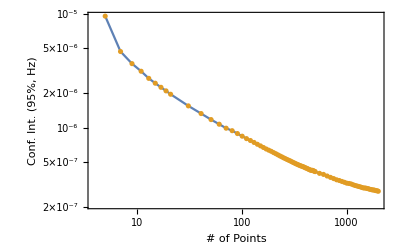

```mathematica
subRangeFitPlot
```

## Verify Fits Generally OK

```mathematica
(*todo: migrate to our TMPFUNCDJ/inspect for ease*)
```

```mathematica
scde0={1,20,-1};
scde1=fitResArrY[[scde0,1]]
```

{5,131,2001}

```mathematica
xranges={peakIndDJ[[1]]-20,peakIndDJ[[1]]+20};
xrangesFreq=dataFFTMag[[xranges,1]];
yPoints=dataFFTMag[[xranges[[1]];;xranges[[2]]]];
```

```mathematica
zz0=ListPlot[
{yPoints},
Joined->{False},
PlotRange->Full
];
zz1=Plot[
#,
{x,xrangesFreq[[1]],xrangesFreq[[2]]},

PlotRange->Full,
PlotLegends->scde1
]&[#[x]&/@fitResArrY[[scde0,2]]];
```

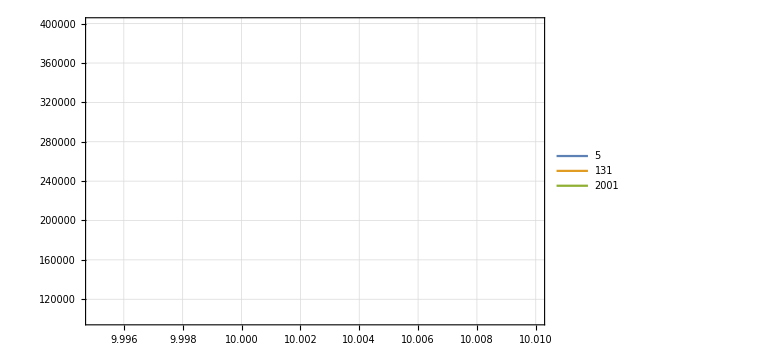

```mathematica
Show[
{zz0,zz1},
PlotRange->{
{9.995,10.010},
{1.*^5,4.*^5}
}
(*PlotRange->Full*)
]
```

# Deprecated

## idk

```mathematica
(*Options[Plot2DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35],
"args"->None
};
(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot2DResults[data_List,OptionsPattern[{Options[Plot2DResults],ListDensityPlot}]]:=Block[
{
AxesLabelVals=OptionValue["AxesLabels"]
},
Return[];
];*)
```

```mathematica
(*(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];*)
```

```mathematica
(*summaryFigure={
(*processed data*)
Show[
ListPlot[
{
dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Black},
ImageSize->Scaled[0.45]
],
fitPlot
],
(*probability data*)
ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black},
ImageSize->Scaled[0.45]
]
};*)
```

## Average Process TMP old

```mathematica
(*dsDJ={
{417978,663.18},
{733291.5,589.2},
{725220.4,562.1},
{760476.1,489.7},
{203208.5,689.9},
{454104.8,731.8},
{586355.2,672.0},
{603545.7,689.4},
{244151.4,668.0},
{490759.4,724.9},
{635202.1,668.0},
{566042.9,680.0},
{152145.4,688.1},
{426735.2,711.4},
{416218.2,730.7},
{478389.4,726.4},
{281069.5,694.9},
{425539.6,692.6},
{499289.5,686.5},
{526815.8,670.1},
{692285.6,624.6},
{79082.0,653.9},
{356972.6,704.5},
{371446.4,779.2},
{460979.0,735.6},
{567344.9,687.2},
{253373.2,685.7},
{529439.4,666.0},
{566810.1,681.7},
{701366.3,671.4},
{631287.9,648.0},
{674851.0,634.1},
{142021.4,718.1},
{275805.8,718.7},
{392675.5,722.1},
{469954.6,722.3},
{433463.0,758.1},
{414991.7,706.0},
{290433.7,706.0},
{507493.8,701.7},
{517923.1,694.1},
{544299.4,657.4},
{600034.0,692.7},
{532569.0,655.8},
{106789.7,614.5},
{200049.6,742.2},
{309311.2,694.2},
{354517.5,733.5},
{351675.0,732.4},
{387582.5,711.0}
};*)
```

```mathematica
(*ListLinePlot[{#,#},Joined->{False,True},PlotRange->Full,ImageSize->Scaled[0.45]]&/@Transpose[dsDJ]
ListLinePlot[{#,#},Joined->{False,True},PlotRange->Full,ImageSize->Scaled[0.45]]&[dsDJ[[;;,1]]/dsDJ[[;;,2]]]*)
```

```mathematica
(*Histogram[#,"FreedmanDiaconis","Probability",ImageSize->Scaled[0.45]]&/@Transpose[dsDJ]
Histogram[#,"FreedmanDiaconis","Probability",ImageSize->Scaled[0.45]]&[dsDJ[[;;,1]]/dsDJ[[;;,2]]]*)
```